```mathematica
Lecture 5: Substitutions, Patterns
```

## Substitutions and Rules

### Exercise Subsection

What does the following cell do?

```mathematica
Clear[x,y]
```

```mathematica
ReplaceAll[x^2+y^2,{x->1,y->x}]
ReplaceRepeated[x^2+y^2,{x->1,y->x}]
x^2+y^2/.{x->1,y->x}
x^2+y^2//.{x->1,y->x}
```

1+x^2

2

1+x^2

2

### Exercise Subsection

What does the following cell do?

```mathematica
ReplaceAll[x^2+1,#]&/@Solve[(x-1)(x-2)(x-3)==0,x]
```

{2,5,10}

```mathematica
Solve[(x-1)(x-2)(x-3)==0,x]
```

{{x→1},{x→2},{x→3}}

## Patterns

The underscore _ matches any expression, x_ matches any expression to be named x .  Two underscores __ match any sequence of one or more expressions and ___ for any sequence of 0 or more expressions .

### Exercise Subsection

What do the following cells do when evaluated?

```mathematica
MatchQ[Range@5,{1,a_,3,_,5}]
```

True

```mathematica
x^2+y^2/.{a_^b_->b^a}
```

2^x+2^y

```mathematica
3 x^2-5x+1/.{a_ x^2+b_ x +c_ -> 2 a x + b}
```

-5+6 x

```mathematica
{{a,b},{c,d},{e,f}}/.{{x_,y_}->x/y}
```

{a/b,c/d,e/f}

```mathematica
MatchQ[{x^2},{_}]
MatchQ[{x^2,x^3,x^5},{_}]
MatchQ[{x^2,x^3,x^5},{__}]
MatchQ[{x^2,x^3,x^5},_]
```

```mathematica
MatchQ[{x^2,x^3},{x^2,x^3,___}]
```

True

### Exercise Subsection

What does the following cell do?

```mathematica
Permutations@Range@3/.{a_,b_,c_}-> x^a  y^b z^c
```

### Exercise Subsection

Produce the same output as the cell below in a few different ways.

```mathematica
Tuples[Range@5,2]/.{a_,b_}->a+I b
```

{1+ⅈ,1+2 ⅈ,1+3 ⅈ,1+4 ⅈ,1+5 ⅈ,2+ⅈ,2+2 ⅈ,2+3 ⅈ,2+4 ⅈ,2+5 ⅈ,3+ⅈ,3+2 ⅈ,3+3 ⅈ,3+4 ⅈ,3+5 ⅈ,4+ⅈ,4+2 ⅈ,4+3 ⅈ,4+4 ⅈ,4+5 ⅈ,5+ⅈ,5+2 ⅈ,5+3 ⅈ,5+4 ⅈ,5+5 ⅈ}

```mathematica
Flatten@Table[a + b I,{a,1,5},{b,1,5}]
```

{1+ⅈ,1+2 ⅈ,1+3 ⅈ,1+4 ⅈ,1+5 ⅈ,2+ⅈ,2+2 ⅈ,2+3 ⅈ,2+4 ⅈ,2+5 ⅈ,3+ⅈ,3+2 ⅈ,3+3 ⅈ,3+4 ⅈ,3+5 ⅈ,4+ⅈ,4+2 ⅈ,4+3 ⅈ,4+4 ⅈ,4+5 ⅈ,5+ⅈ,5+2 ⅈ,5+3 ⅈ,5+4 ⅈ,5+5 ⅈ}

```mathematica
Permutations[Range@5,{2}]/.{a_,b_}->a+I b
```

{1+2 ⅈ,1+3 ⅈ,1+4 ⅈ,1+5 ⅈ,2+ⅈ,2+3 ⅈ,2+4 ⅈ,2+5 ⅈ,3+ⅈ,3+2 ⅈ,3+4 ⅈ,3+5 ⅈ,4+ⅈ,4+2 ⅈ,4+3 ⅈ,4+5 ⅈ,5+ⅈ,5+2 ⅈ,5+3 ⅈ,5+4 ⅈ}

### Exercise Subsection

What does the following code do?

```mathematica
X=x^Range[5,10]
X=X/.x^a_->a x^(a-1)
X/.Power->Plus
```

{x^5,x^6,x^7,x^8,x^9,x^10}

{5 x^4,6 x^5,7 x^6,8 x^7,9 x^8,10 x^9}

{5 (4+x),6 (5+x),7 (6+x),8 (7+x),9 (8+x),10 (9+x)}

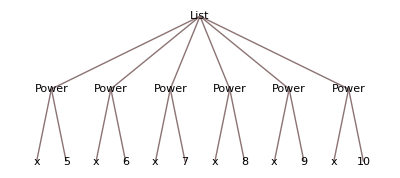

```mathematica
TreeForm@X
```

### Exercise Subsection

The /; modifier gives conditions on the pattern.  It plays the role of “such that” in mathematics.  What do the following cells do when evaluated?

```mathematica
L=Range[10,20]
L/.{x_/;x>5->x^2}
```

{10,11,12,13,14,15,16,17,18,19,20}

{100,121,144,169,196,225,256,289,324,361,400}

```mathematica
DeleteCases[L,x_/;x>5]
Cases[L,x_/;x>5]
Select[L,MatchQ[x_/;x>5]]
```

{1,2,3,4,5}

{6,7,8,9,10}

{6,7,8,9,10}

```mathematica
L
Position[L,x_/;PrimeQ[x]]
Count[L,x_/;x>5]
```

{10,11,12,13,14,15,16,17,18,19,20}

{{2},{4},{8},{10}}

11

```mathematica
RandomInteger[{-4,4},10]/.{a_/;Positive[a]->x,b_/;Negative[b]->34}
```

{x,x,34,0,x,x,x,34,x,34}

### Exercise Subsection

The pattern  _h matches any expression with head h and _?F can be used to check if F is True or False.
What do the following cells do when evaluated?

```mathematica
fac[n_Integer/;n>=0]:=n!
```

```mathematica
fac[5.9]
```

fac[5.9]

```mathematica
Cases[Range@15,_?EvenQ]
```

```mathematica
DeleteCases[Range@20,p_?PrimeQ]
```

```mathematica
Clear[f]
```

```mathematica
f[n_Integer/;EvenQ[n]]:=n
f[n_Integer/;OddQ[n]]:=n+1
```

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
NoRepeats[L_List/;Length@L>0]:=L//.{x___,a_,y___,a_,z___}->{x,a,y,z}
```

```mathematica
NoRepeats[{{1,2,3,3},{1,4}}]
```

{{1,2,3},{1,4}}

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
L=RandomSample@Range@100
L//.{x___,a_,b_,y___}/;b<a->{x,b,a,y}
```

{46,1,51,86,92,14,25,34,78,72,97,8,75,41,12,71,98,38,70,37,84,53,3,27,62,6,28,23,15,22,43,18,77,17,54,58,61,52,59,73,67,21,40,56,45,65,35,47,20,79,49,90,87,33,5,26,83,100,76,64,30,7,11,2,74,39,85,95,24,13,19,16,42,80,93,89,94,63,57,82,10,91,60,36,55,4,69,9,44,96,66,50,48,31,88,99,81,32,29,68}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

### Exercise Subsection

The NSolve function produces a list of rules that solve the given equation, for example, consider the next cell.

```mathematica
solutions=NSolve[1320-3092 x+2338 x^2-571 x^3+17 x^4-28 x^5+21 x^6-5 x^7-60 x^21+140 x^22-105 x^23+25 x^24-12 x^55+28 x^56-21 x^57+5 x^58== 0, x]
```

{{x→-1.08967-0.0672631 ⅈ},{x→-1.08967+0.0672631 ⅈ},{x→-1.06919-0.182733 ⅈ},{x→-1.06919+0.182733 ⅈ},{x→-1.05052-0.307232 ⅈ},{x→-1.05052+0.307232 ⅈ},{x→-0.999016-0.427734 ⅈ},{x→-0.999016+0.427734 ⅈ},{x→-0.950112-0.530761 ⅈ},{x→-0.950112+0.530761 ⅈ},{x→-0.882774-0.6454 ⅈ},{x→-0.882774+0.6454 ⅈ},{x→-0.797737-0.73332 ⅈ},{x→-0.797737+0.73332 ⅈ},{x→-0.718481-0.823261 ⅈ},{x→-0.718481+0.823261 ⅈ},{x→-0.610472-0.902379 ⅈ},{x→-0.610472+0.902379 ⅈ},{x→-0.510175-0.958089 ⅈ},{x→-0.510175+0.958089 ⅈ},{x→-0.396897-1.02005 ⅈ},{x→-0.396897+1.02005 ⅈ},{x→-0.272459-1.05044 ⅈ},{x→-0.272459+1.05044 ⅈ},{x→-0.160359-1.07853 ⅈ},{x→-0.160359+1.07853 ⅈ},{x→-0.0267638-1.09228 ⅈ},{x→-0.0267638+1.09228 ⅈ},{x→0.0918091-1.08016 ⅈ},{x→0.0918091+1.08016 ⅈ},{x→0.215108-1.0726 ⅈ},{x→0.215108+1.0726 ⅈ},{x→0.341553-1.03276 ⅈ},{x→0.341553+1.03276 ⅈ},{x→0.447312-0.990583 ⅈ},{x→0.447312+0.990583 ⅈ},{x→0.566884-0.935562 ⅈ},{x→0.566884+0.935562 ⅈ},{x→0.663501-0.856745 ⅈ},{x→0.663501+0.856745 ⅈ},{x→0.757412-0.785904 ⅈ},{x→0.757412+0.785904 ⅈ},{x→0.847429-0.686165 ⅈ},{x→0.847429+0.686165 ⅈ},{x→0.910382-0.58886 ⅈ},{x→0.910382+0.58886 ⅈ},{x→0.981485-0.48369 ⅈ},{x→0.981485+0.48369 ⅈ},{x→1.},{x→1.02406-0.360859 ⅈ},{x→1.02406+0.360859 ⅈ},{x→1.05934-0.252088 ⅈ},{x→1.05934+0.252088 ⅈ},{x→1.08372},{x→1.08649-0.121227 ⅈ},{x→1.08649+0.121227 ⅈ},{x→1.2},{x→2.}}

Use a pattern and to change the variable solutions to a list of complex numbers instead of a list of rules.  Then, use a pattern and use Cases to select those values that are real.

```mathematica
Cases[solutions/.{x->a_}->a,a_/;Element[a,Reals]]
```

{1.,1.08372,1.2,2.}

### Exercise Subsection

Use Cases and patterns to define a function that returns the permutations of n (use Permutations@Range@n) such that the 1 appears before the 2 and the 2 appears before the 3 such that the 2 and the 3 are not consecutive.

```mathematica
Cases[Permutations@Range@5,{___,1,___,2,__,3,___}]
```

{{1,2,4,3,5},{1,2,4,5,3},{1,2,5,3,4},{1,2,5,4,3},{1,4,2,5,3},{1,5,2,4,3},{4,1,2,5,3},{5,1,2,4,3}}

```mathematica
MatchQ[{5,6,2,1,4,7,3,8},{___,a_,___,b_,___,c_,___,d_,___}/;And[a<c,c<d,d<b]]
```

False

### Exercise Subsection

Find the first prime number that does not appear as consecutive digits in the first 10000 decimal digits of Pi.

```mathematica
FindInPi[n_Integer]:=Position[Partition[First@RealDigits[Pi,10,10000],Length@IntegerDigits@n,1],IntegerDigits@n]
```

```mathematica
n=2;
While[FindInPi[n]!={},n=NextPrime[n]]
n
```

### Exercise Subsection

Define a function Subwords[word_] that finds all words in WordList[] that contain the (possibly nonconsecutive) letters of the string “word” in order.  For example, consider the next cell.

```mathematica
Subwords["mathy"]
```

{amateurishly,aromatherapy,chromatography,cinematography,empathy,homeopathy,magnetohydrodynamics,mathematically,matriarchy,misanthropy,sympathetically,sympathy,unsympathetically}

```mathematica
Subwords[word_]:=Select[WordList[],MatchQ[Characters@#,Join[{___},Riffle[Characters@word,___],{___}]]&]
```

```mathematica
Subwords["jesse"]
```

{joylessness}

```mathematica
Characters@"math"
```

{m,a,t,h}

To match the word “mathy”, the pattern would be the following

```mathematica
{___,m,___,a,___,t,___,h,___,y,___}
```

```mathematica
Riffle[Characters@"mathy",___]
```

{m,___,a,___,t,___,h,___,y}

### Exercise Subsection

A bit string of length n is a list of 0’s and 1’s of length n.  All bit strings can be created by Tuples[{0,1},n].  How many bit strings of length n contain the consecutive bits 1,0,1 for n = 3,...,15?

## Regular Expressions

Regular expressions are a common construct for matching strings in many programming languages.  See RegularExpression in the documentation for the syntax.

```mathematica
?RegularExpression
```

### Exercise Subsection

Use Select with StringMatchQ and RegularExpression to find the words in WordList[] that do not use any of the letters a,e,i,o,u (neither upper nor lowercase).

```mathematica
Select[WordList[],StringMatchQ[#,RegularExpression["[^aeiouAEIOU]*"]]&]
```

{by,cry,crypt,cyst,dB,dry,dryly,fly,fry,glyph,gym,gypsy,h'm,hm,hymn,kc,kHz,kph,kW,lymph,lynch,lynx,ms,my,myrrh,myth,nth,nymph,pH,ply,pry,psst,pygmy,pyx,rhythm,sh,shh,shy,shyly,sky,sly,slyly,spry,spy,sty,sylph,sync,thy,TNT,try,tryst,TV,why,wry,wryly}

### Exercise Subsection

Use RegularExpressions to find the words in WordList[] that contain consecutive repeated letter ww’s.

```mathematica
Select[WordList[],StringMatchQ[#,RegularExpression[".*vv.*"]]&]
```

{chivvy,civvies,divvy,navvy,savvy,skivvy}

### Exercise Subsection

Use Select with StringMatchQ and RegularExpression to find the 10 longest words in WordList[] that begin and end with a vowel (one of “aeiou”).

```mathematica
Sort[{StringLength@#,#}&/@Select[WordList[],StringMatchQ[#,RegularExpression["[aeiou]+.*[aeiou]+"]]&]][[-10;;]]
```

{{15,unsportsmanlike},{16,incomprehensible},{16,incontrovertible},{16,inextinguishable},{16,institutionalize},{16,intercommunicate},{16,internationalize},{16,unrepresentative},{17,indistinguishable},{17,ultraconservative}}

### Exercise Subsection

What are the longest words in WordList[] that does not use the letter e.?

```mathematica
Last/@Select[Sort[{StringLength@#,#}&/@Select[WordList[],StringMatchQ[#,RegularExpression["[^e].*"]]&]],First@#==20&]
```

{buckminsterfullerene,compartmentalization,counterrevolutionary,internationalization,magnetohydrodynamics,uncharacteristically}

```mathematica
Select[WordList[],StringMatchQ[#,RegularExpression["[^e]*"]]&]
```